# Resultados prácticas

Amado Cabrera

## Importando cosas

```mathematica
Get[NotebookDirectory[]<>"../DTQW.wl"]
MatrixPartialTrace=ResourceFunction["MatrixPartialTrace"];
<<MaTeX`
```

## Definiendo variables

```mathematica
clrso=RGBColor[#]&/@({"#d8d97a","#95c36e","#74c8c3","#5a97c1","#295384","#0a2e57"});
clrs=RGBColor[#]&/@({"#d8d97a","#95c36e","#74c8c3","#5a97c1","#295384","#0a2e57"}[[{4,2,5,3,1,6}]]);
```

```mathematica
qlabels=MaTeX[#,
Magnification->1.4,
"Preamble"->{"\\usepackage{physics}"}
]&/@{"\\text{Posición }\\ket{x}","\\text{Probabilidad }\\mel{x}{\\rho_X}{x}"};
clabels=MaTeX[#,
Magnification->1.4,
"Preamble"->{"\\usepackage{physics}"}
]&/@{"\\text{Posición }x","\\text{Probabilidad }P(x)"};
plotargs={
BaseStyle->{FontFamily->"LM Roman 12",FontSize->15},
Axes->False,
Frame->True,
Mesh->All,
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,Opacity[0.5]]
};
```

```mathematica
TeXLabel[tlist_List]:=MaTeX[
"\\begin{gathered}\n"<>Fold[
StringJoin[#1,"\\\\\n",#2]&,ToString@StringForm["\\text{``}",#]&/@tlist
]<>"\n\\end{gathered}",
FontSize->14,
Magnification->1.3,
"Preamble"->{"\\usepackage{physics}"}
]
```

## Inicializaciones

```mathematica
dimensions={2,201};
InitializeDTQW@@dimensions;
MakeCoin[1/2,0,0];
MakeShift[];
MakeUnitary[];
```

## Resultados

### Caminatas sin decoherencia

#### Base computacional

```mathematica
prob00=Module[
{psi0,rho},
psi0=VectorState[{{1,0,0}}];
rho=#.#†&@DTQW2[psi0,100];
Diagonal@MatrixPartialTrace[rho,1,dimensions]
];
```

```mathematica
prob10=Module[
{psi0,rho},
psi0=VectorState[{{1,1,0}}];
rho=#.#†&@DTQW2[psi0,100];
Diagonal@MatrixPartialTrace[rho,1,dimensions]
];
```

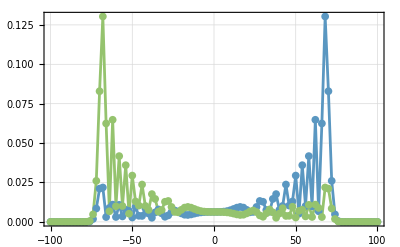

```mathematica
pltcomp=ListLinePlot[(Transpose[{Range[-100,100],#}][[;;;;2]])&/@{prob00,prob10},
plotargs,
PlotRange->All,
PlotStyle->clrs,
FrameLabel->qlabels,
PlotLegends->(MaTeX[#,
Magnification->1.25,
"Preamble"->{"\\usepackage{physics}"}
]&/@{"\\ket{0,0}","\\ket{1,0}"})
]
```

```mathematica
Export[NotebookDirectory[]<>"results-decoherence/pltcomp.pdf",pltcomp]
```

/home/amadoc/Desktop/Programming/Mathematica/quantum_walks/AmadoTemp/practicas/results-decoherence/pltcomp.pdf

#### Estado equiprobable +_y

```mathematica
probpy0=Module[
{psi0,rho},
psi0=VectorState[{{1/Sqrt[2],0,0},{ⅈ/Sqrt[2],1,0}}];
rho=#.#†&@DTQW2[psi0,100];
Diagonal@MatrixPartialTrace[rho,1,dimensions]
];
```

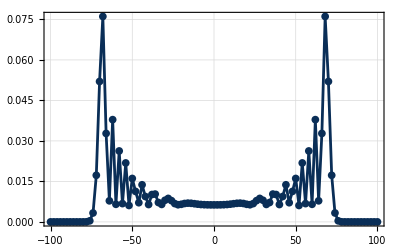

```mathematica
pltpy0=ListLinePlot[Transpose[{Range[-100,100],probpy0}][[;;;;2]],
plotargs,
PlotRange->All,
PlotStyle->clrs,
FrameLabel->qlabels
]
```

```mathematica
Export[NotebookDirectory[]<>"results-decoherence/pltpy0.pdf",pltpy0]
```

/home/amadoc/Desktop/Programming/Mathematica/quantum_walks/AmadoTemp/practicas/results-decoherence/pltpy0.pdf

### Caminatas con decoherencia

#### Primer resultado

```mathematica
probwd0=Module[
{psi0,rho},
psi0=VectorState[{{1/Sqrt[2],0,0},{ⅈ/Sqrt[2],1,0}}];
rho=DTQW2wDecoherence[psi0,0.99,100];
Diagonal@MatrixPartialTrace[rho,1,dimensions]
];
```

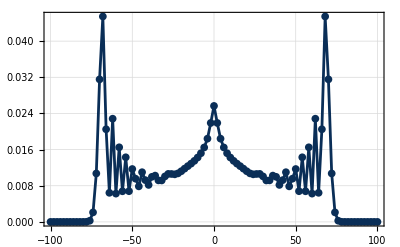

```mathematica
pltwd0=ListLinePlot[Transpose[{Range[-100,100],probwd0}][[;;;;2]],
plotargs,
PlotRange->All,
PlotStyle->clrs,
FrameLabel->qlabels
]
```

```mathematica
Export[NotebookDirectory[]<>"results-decoherence/pltwd0.pdf",pltwd0]
```

/home/amadoc/Desktop/Programming/Mathematica/quantum_walks/AmadoTemp/practicas/results-decoherence/pltwd0.pdf

#### Gradiente de decoherencia

```mathematica
probwdG=Module[
{psi0,rho},
psi0=VectorState[{{1/Sqrt[2],0,0},{ⅈ/Sqrt[2],1,0}}];
rho=DTQW2wDecoherence[psi0,1-#,100]&/@Range[0,1,0.2];
Diagonal@MatrixPartialTrace[#,1,dimensions]&/@rho
];
```

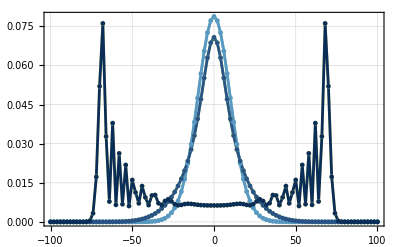

```mathematica
pltwdG=ListLinePlot[(Transpose[{Range[-100,100],#}][[;;;;2]])&/@probwdG,
plotargs,
PlotRange->All,
PlotStyle->clrso,
FrameLabel->qlabels,
PlotLegends->(MaTeX[q==#,
Magnification->1.25
]&/@Range[0,1,0.2])
]
```

```mathematica
Export[NotebookDirectory[]<>"results-decoherence/pltwdG.pdf",pltwdG]
```

/home/amadoc/Desktop/Programming/Mathematica/quantum_walks/AmadoTemp/practicas/results-decoherence/pltwdG.pdf

#### Zoom al gradiente de decoherencia

```mathematica
probwdZ=Module[
{psi0,rho},
psi0=VectorState[{{1/Sqrt[2],0,0},{ⅈ/Sqrt[2],1,0}}];
rho=DTQW2wDecoherence[psi0,1-#,100]&/@Range[0.02,0.1,0.02];
Diagonal@MatrixPartialTrace[#,1,dimensions]&/@rho
];
```

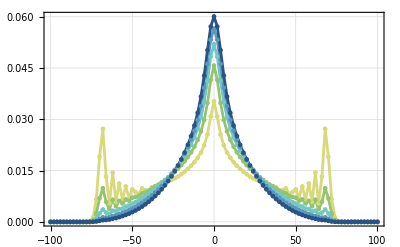

```mathematica
pltwdZ=ListLinePlot[(Transpose[{Range[-100,100],#}][[;;;;2]])&/@probwdZ,
plotargs,
PlotRange->All,
PlotStyle->clrso,
FrameLabel->qlabels,
PlotLegends->(MaTeX[q==#,
Magnification->1.25
]&/@Range[0.02,0.1,0.02])
]
```

```mathematica
Export[NotebookDirectory[]<>"results-decoherence/pltwdZ.pdf",pltwdZ]
```

/home/amadoc/Desktop/Programming/Mathematica/quantum_walks/AmadoTemp/practicas/results-decoherence/pltwdZ.pdf

#### Decoherencia de 0.5

```mathematica
probwdc=Module[
{psi0,rho},
psi0=VectorState[{{1/Sqrt[2],0,0},{ⅈ/Sqrt[2],1,0}}];
rho=DTQW2wDecoherence[psi0,0.5,100];
Diagonal@MatrixPartialTrace[rho,1,dimensions]
];
```

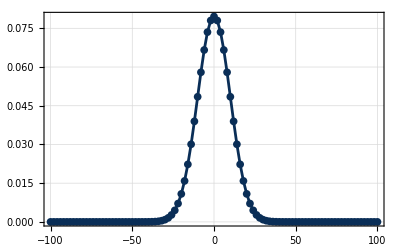

```mathematica
pltwdc=ListLinePlot[(Transpose[{Range[-100,100],probwdc}][[;;;;2]]),
plotargs,
PlotRange->All,
PlotStyle->clrso,
FrameLabel->qlabels
]
```

```mathematica
Export[NotebookDirectory[]<>"results-decoherence/pltwdc.pdf",pltwdc]
```

/home/amadoc/Desktop/Programming/Mathematica/quantum_walks/AmadoTemp/practicas/results-decoherence/pltwdc.pdf

#### Caminata clásica

```mathematica
probclassic=Riffle[Binomial[#,Range[0,#]]/2^#,0]&@100//N//Chop;
```

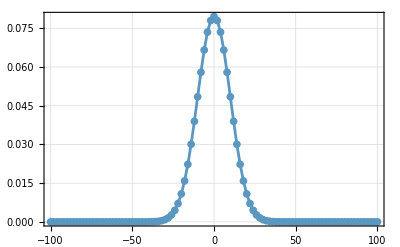

```mathematica
pltclassic=ListLinePlot[Transpose[{Range[-100,100],probclassic}][[;;;;2]],
plotargs,
PlotRange->All,
PlotStyle->Reverse[clrs],
FrameLabel->clabels
]
```

```mathematica
Export[NotebookDirectory[]<>"results-decoherence/pltclassic.pdf",pltclassic]
```

/home/amadoc/Desktop/Programming/Mathematica/quantum_walks/AmadoTemp/practicas/results-decoherence/pltclassic.pdf

#### Diferencia entre RW y DTQW w/d

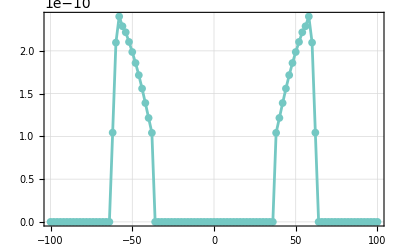

```mathematica
pltdiff=ListLinePlot[Transpose[{Range[-100,100],#}][[;;;;2]]&@Chop@Abs[probwdc-probclassic],
plotargs,
PlotRange->All,
PlotStyle->clrs[[4]],
FrameLabel->(MaTeX[#,
Magnification->1.4,
"Preamble"->{"\\usepackage{physics}"}
]&/@{"\\text{Posición }x","\\text{Diferencias}"})
]
```

```mathematica
Export[NotebookDirectory[]<>"results-decoherence/pltdiff.pdf",pltdiff]
```

/home/amadoc/Desktop/Programming/Mathematica/quantum_walks/AmadoTemp/practicas/results-decoherence/pltdiff.pdf

#### Gradiente de decoherencia

```mathematica
probwdG2=Module[
{psi0,rho},
psi0=VectorState[{{1,0,0}}];
rho=DTQW2wDecoherence[psi0,1-#,100]&/@Range[0,1,0.2];
Diagonal@MatrixPartialTrace[#,1,dimensions]&/@rho
];
```

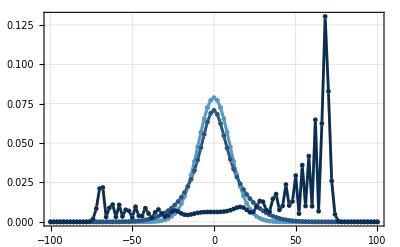

```mathematica
pltwdG2=ListLinePlot[(Transpose[{Range[-100,100],#}][[;;;;2]])&/@probwdG2,
plotargs,
PlotRange->All,
PlotStyle->clrso,
FrameLabel->qlabels,
PlotLegends->(MaTeX[q==#,
Magnification->1.25
]&/@Range[0,1,0.2])
]
```

```mathematica
Export[NotebookDirectory[]<>"results-decoherence/pltwdG2.pdf",pltwdG2]
```

/home/amadoc/Desktop/Programming/Mathematica/quantum_walks/AmadoTemp/practicas/results-decoherence/pltwdG.pdf

## unimportant

```mathematica
trash1=ListLinePlot[Transpose[{Range[-100,100],probclassic}][[;;;;2]],
plotargs,
PlotRange->All,
PlotStyle->Reverse[clrs],
FrameLabel->qlabels
]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"results-decoherence/trash1.pdf",trash1]
```

/home/amadoc/Desktop/Programming/Mathematica/quantum_walks/AmadoTemp/practicas/results-decoherence/trash1.pdf